### NDSolve Module

```mathematica
(*Here we create a function that solves the equations of motion in discrete sections, defined when each constaint goes to zero*)
solvestep[L_,t0_,θ0_,ϕ0_,α0_,dθ0_,dϕ0_,dα0_,tguess_,tf_, constraints_]:=(
(*Add the constraints*)
L1=L;
For[i=1,i≤ Length[constraints],i++,
L1=L1+constraints[[i]][[1]] constraints[[i]][[2]];];
sol= {};
(*NDSolve based on how many constraints*)
Which[Length[constraints]==2,
sol=NDSolve[{EL[L1,θ],EL[L1,ϕ],EL[L1,α],(*first solve with two constraints*)
α[t0]==α0,
α'[t0]==dα0,
θ[t0]==θ0,
θ'[t0]==dθ0,
ϕ[t0]==ϕ0,
ϕ'[t0]==dϕ0,
D[constraints[[1,2]],t,t]==0,
D[constraints[[2,2]],t,t]==0},
{θ[t],ϕ[t],α[t],constraints[[1,1]],constraints[[2,1]]},{t,t0,tf}],
Length[constraints]==1,
sol = NDSolve[{EL[L1,θ],EL[L1,ϕ],EL[L1,α],(*then solve with one constraint*)
α[t0]==α0,
α'[t0]==dα0,
θ[t0]==θ0,
θ'[t0]==dθ0,
ϕ[t0]==ϕ0,
ϕ'[t0]==dϕ0,
D[constraints[[1,2]],t,t]==0},
{θ[t],ϕ[t],α[t],constraints[[1,1]]},{t,t0,tf}],
Length[constraints]==0,
sol = NDSolve[{EL[L1,θ],EL[L1,ϕ],EL[L1,α], (*finally solve with no constraints*)
α[t0]==α0,
α'[t0]==dα0,
θ[t0]==θ0,
θ'[t0]==dθ0,
ϕ[t0]==ϕ0,
ϕ'[t0]==dϕ0},
{θ[t],ϕ[t],α[t]},{t,t0,tf}]];
(*Pull off solutions*)
solnlist = {};
For[i = 1, i≤Length[sol[[1]]],i++,
AppendTo[solnlist, sol[[1,i,2]]]; 
];
(*Obtain first zeros so we can identify when each constraint goes to zero and splice them together later*)
zeros={};
For[i=4, i≤Length[solnlist],i++,
AppendTo[zeros,
FindRoot[solnlist[[i]],{t,tguess}]];
];
(*Return solutions and zeros*)
Return[{solnlist,zeros}];
)
```

## Kinetic energy

```mathematica
Clear[T,U,mb,mcw,ma,IIa,l1,l2,h,r,g,θ,ϕ,α,L,t,tf,EL,soln,xb,yb,xcw,ycw,xcma,ycma,λ,γ,G1,G2,x,y]
```

```mathematica
T:= 1/2 mb(D[xb,t]^2+D[yb,t]^2) + 1/2 mcw(D[xcw,t]^2+D[ycw,t]^2)+1/2 IIa D[θ[t],t]^2
```

```mathematica
IIa:=1/3 ma ((l1^3+l2^3)/(l1+l2))(*Moment of Inertia of the throwing arm*)
```

### Potential energy

```mathematica
U:= mb g yb+mcw g ycw+ma g ycma
```

### Define transformation to generalized coordinates

These are also defined later on in the notebook

```mathematica
xb:= l1 Cos[θ[t]]+r Cos[ϕ[t]](*these are barrel coord*)
yb:=-l1 Sin[θ[t]]-r Sin[ϕ[t]]
xcw:=-l2 Cos[θ[t]]+h Cos[α[t]](*these are counter-weight coord*)
ycw:=l2 Sin[θ[t]]-h Sin[α[t]]
ycma:=-(l1-l2)/2 Sin[θ[t]](*these are center of mass coord*)
```

### Define Constraint Functions:

```mathematica
G1:= θ[t]-α[t]+α[0](*counter weight*)
```

```mathematica
G2:=θ[t]-ϕ[t]+ϕ[0](*barrel*)
```

```mathematica
Simplify[T]
```

1/6 (3 h^2 mcw α'[t]^2-6 h l2 mcw Cos[α[t]-θ[t]] α'[t] θ'[t]+(-l1 l2 ma+l1^2 (ma+3 mb)+l2^2 (ma+3 mcw)) θ'[t]^2+6 l1 mb r Cos[θ[t]-ϕ[t]] θ'[t] ϕ'[t]+3 mb r^2 ϕ'[t]^2)

```mathematica
Simplify[U]
```

-1/2 g (2 h mcw Sin[α[t]]+(l1 (ma+2 mb)-l2 (ma+2 mcw)) Sin[θ[t]]+2 mb r Sin[ϕ[t]])

#### Define L

```mathematica
L:= T - U
```

```mathematica
Simplify[L]
```

1/6 (3 h^2 mcw α'[t]^2-6 h l2 mcw Cos[α[t]-θ[t]] α'[t] θ'[t]+(-l1 l2 ma+l1^2 (ma+3 mb)+l2^2 (ma+3 mcw)) θ'[t]^2+6 l1 mb r Cos[θ[t]-ϕ[t]] θ'[t] ϕ'[t]+3 (g (2 h mcw Sin[α[t]]+(l1 (ma+2 mb)-l2 (ma+2 mcw)) Sin[θ[t]]+2 mb r Sin[ϕ[t]])+mb r^2 ϕ'[t]^2))

```mathematica
(*define constants*)
g:=9.81
mb:=0.5
mcw:=20
ma:=1
l1:=3
l2:=1
h:=3
r:=1
```

```mathematica
EL[L_,x_] :=D[L,x[t]]-D[L,x'[t],t]==0;
```

```mathematica
Clear[L1,solnlist,zeros,sol,constraints1, tf];
```

```mathematica
tf=10;
```

```mathematica
(*constraints present in the first step*)
constraints1={{λ[t],G1},{γ[t],G2}};
```

```mathematica
(*solving the first step, up till first constraint goes away*)
step1 = solvestep[L,0,0,Pi,7Pi/4,0,0,0,0.5,tf,constraints1]
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

{{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{{t→0.626966},{t→0.770141}}}

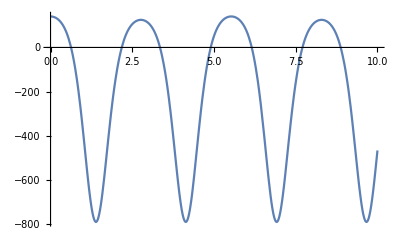

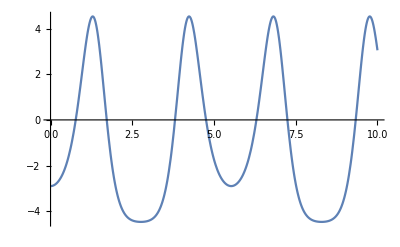

```mathematica
Plot[step1[[1,4]],{t,0,tf}]
Plot[step1[[1,5]],{t,0,tf}]
(*plotting constraints over entire time*)
```

```mathematica
Print[step1[[2]]] (*these are the zeros*)
```

{{t→0.626966},{t→0.770141}}

```mathematica
Clear[L2,solnlist,zeros,constraints2,sol,t2,step2];
```

```mathematica
constraints2={{γ[t],G2}};
```

```mathematica
t2=step1[[2,1,1,2]];
(*isolating when constraint 1 goes to 0 to find where to splice together*)
Print[t2];
```

0.626966

```mathematica
step2 = solvestep[L,t2,step1[[1,1,0]][t2],step1[[1,2,0]][t2],step1[[1,3,0]][t2],step1[[1,1,0]]'[t2],step1[[1,2,0]]'[t2],step1[[1,3,0]]'[t2],1,tf, constraints2]
(*same as above for 2nd step (w/o constraint 1)*)
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

InterpolatingFunction::dmval: Input value {-5.70188} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.329812} lies outside the range of data in the interpolating function. Extrapolation will be used.

{{InterpolatingFunction[{{0.626966, 10.}}, <>][t],InterpolatingFunction[{{0.626966, 10.}}, <>][t],InterpolatingFunction[{{0.626966, 10.}}, <>][t],InterpolatingFunction[{{0.626966, 10.}}, <>][t]},{{t→0.655253}}}

```mathematica
Plot[step2[[1,4]],{t,t2,t3}]
```

Plot::plln: Limiting value t3 in {t,0.626966,t3} is not a machine-sized real number.

Plot[step2⟦1,4⟧,{t,t2,t3}]

```mathematica
Print[step2[[2]]]
```

{{t→0.655253}}

```mathematica
Clear[L1,solnlist,zeros,constraints3,sol,t3];
```

```mathematica
constraints3={};
```

```mathematica
t3=step2[[2,1,1,2]];
Print[t3]
```

0.655253

```mathematica
step3 = solvestep[L,t3,step2[[1,1,0]][t3],step2[[1,2,0]][t3],step2[[1,3,0]][t3],step2[[1,1,0]]'[t3],step2[[1,2,0]]'[t3],step2[[1,3,0]]'[t3],2,tf, constraints3]
(*doing the same as above two with only the last constraint*)
```

{{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{}}

```mathematica
Clear[L1,solnlist,zeros,constraints4,sol,t4];
```

```mathematica
t4=FindRoot[Sin[step3[[1,1]]]==-1,{t,1.7}][[1,2]]
```

InterpolatingFunction::dmval: Input value {0.430362} lies outside the range of data in the interpolating function. Extrapolation will be used.

1.44356

```mathematica
θstop =step3[[1,1,0]][t4]
```

4.71239

```mathematica
G3:=θ[t]-θ[t4];
```

```mathematica
constraints4={{β[t],G3}};
```

```mathematica
step4=solvestep[L,t4,step3[[1,1,0]][t4],step3[[1,2,0]][t4],step3[[1,3,0]][t4],0,step3[[1,2,0]]'[t4],step3[[1,3,0]]'[t4],2,tf, constraints4]
(*doing same as above for system without constraints*)
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

{{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{{t→2.31523}}}

#### Stitching the motion together into piece-wise function

```mathematica
θpw[t_]=Piecewise[{{step1[[1,1]], 0≤t<t2}, {step2[[1,1]], t2≤t<t3}, {step3[[1,1]], t3≤t≤t4}, {step4[[1,1]], t4≤t≤tf}}];
```

```mathematica
ϕpw[t_]=Piecewise[{{step1[[1,2]], 0≤t<t2}, {step2[[1,2]], t2≤t<t3}, {step3[[1,2]], t3≤t≤t4}, {step4[[1,2]], t4≤t≤tf}}];
```

```mathematica
αpw[t_]=Piecewise[{{step1[[1,3]], 0≤t<t2}, {step2[[1,3]], t2≤t<t3}, {step3[[1,3]], t3≤t≤t4}, {step4[[1,3]], t4≤t≤tf}}];
```

```mathematica
λpw[t_]=Piecewise[{{step1[[1,4]], 0≤t<t2}, {0, t2≤t<t3}, {0, t3≤t≤t4}, {0, t4≤t≤tf}}];
```

```mathematica
γpw[t_]=Piecewise[{{step1[[1,5]], 0≤t<t2}, {step2[[1,4]], t2≤t<t3}, {0, t3≤t≤t4}, {0, t4≤t≤tf}}];
```

```mathematica
θpw[0]
```

0.

```mathematica
θpw[t4]
```

4.71239

#### Plots of each angles over time and their angular velocities (also constraints)

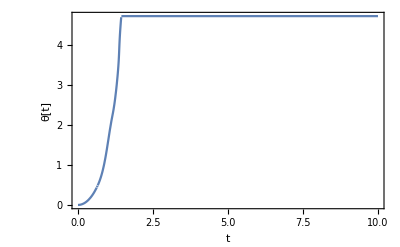

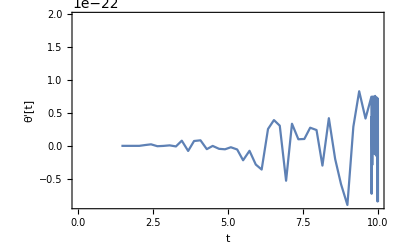

```mathematica
Plot[θpw[t],{t,0,tf},Frame->True,FrameLabel->{"t","θ[t]","Throwing Arm Angle"}]
Plot[θpw'[t],{t,0,tf},Frame->True,FrameLabel->{"t","θ'[t]","Throwing Arm Angular Velocity"}]
```

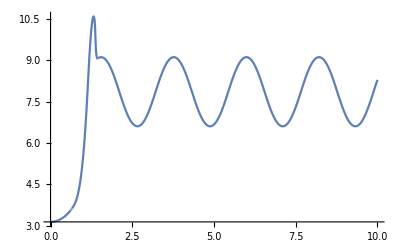

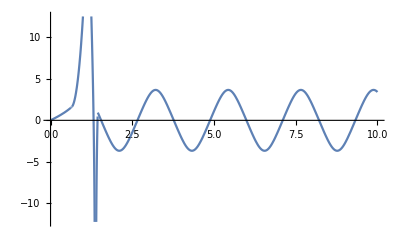

```mathematica
Plot[ϕpw[t],{t,0,tf},PlotLegends->"Expressions"]
Plot[ϕpw'[t],{t,0,tf},PlotLegends->"Expressions"]
```

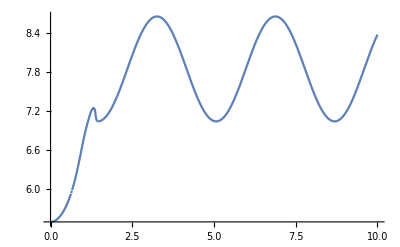

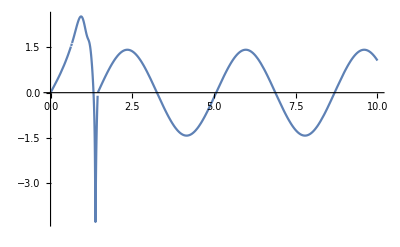

```mathematica
Plot[αpw[t],{t,0,tf},PlotLegends->"Expressions"]
Plot[αpw'[t],{t,0,tf},PlotLegends->"Expressions"]
```

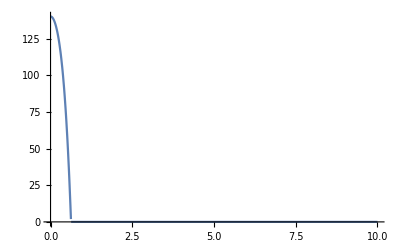

```mathematica
Plot[λpw[t],{t,0,tf},PlotLegends->"Expressions"]
```

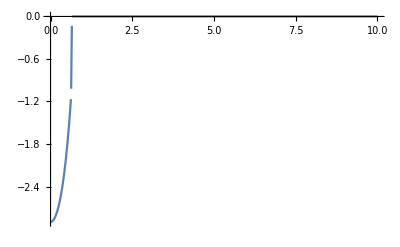

```mathematica
Plot[γpw[t],{t,0,tf},PlotRange->All]
```

#### Redefining x,y coordinates with respect to the new piece-wise functions

```mathematica
xtapp[t_]=l1 Cos[θpw[t]];
ytapp[t_]=-l1 Sin[θpw[t]];
xtacp[t_]=-l2 Cos[θpw[t]];
ytacp[t_]=l2 Sin[θpw[t]];
```

```mathematica
xbp[t_]= l1 Cos[θpw[t]]+r Cos[ϕpw[t]];(*these are barrel coord*)
ybp[t_]=-l1 Sin[θpw[t]]-r Sin[ϕpw[t]];
xcwp[t_]=-l2 Cos[θpw[t]]+h Cos[αpw[t]];(*these are counter-weight coord*)
ycwp[t_]=l2 Sin[θpw[t]]-h Sin[αpw[t]];
tlaunch=1.38 (*estimated time of launch*)
(*including the projectile below*)
xbtotal[t_]=Piecewise[{{xbp[t], 0≤t≤tlaunch}, {xbp'[tlaunch] (t-tlaunch)+xbp[tlaunch], tlaunch<t≤tf}}];
ybtotal[t_]=Piecewise[{{ybp[t], 0≤t≤tlaunch}, {ybp'[tlaunch] (t-tlaunch) -g/2(t-tlaunch)^2+ybp[tlaunch], tlaunch<t ≤tf}}];
```

1.38

1.65

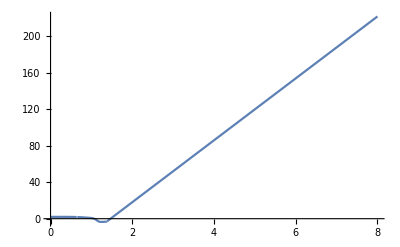

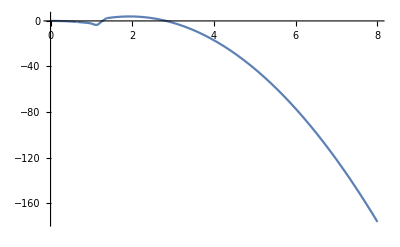

```mathematica
1.65
(*plotting path of projectile as function of time*)
Plot[xbtotal[t],{t,0,8}]
Plot[ybtotal[t],{t,0,8}]
```

#### Animation of system firing with projectile

```mathematica
Manipulate[Graphics[{
Line[{{-6,-6},{-6,6}}],
Line[{{-6,6},{6,6}}],
Blue,Line[{{xtapp[t],ytapp[t]},{xtacp[t],ytacp[t]}}],
Black,Line[{{xtapp[t],ytapp[t]},{xbp[t],ybp[t]}}],
Red,Line[{{xtacp[t],ytacp[t]},{xcwp[t],ycwp[t]}}],
Black,Line[{{-4,-6},{0,0}}],
Black,Line[{{0,0},{4,-6}}],
Black,Line[{{-4,-6},{4,-6}}],
Red,Rectangle[{xcwp[t]-.5,ycwp[t]-.5},{xcwp[t]+.5,ycwp[t]+.5}],
Darker[Green], Circle[{xbtotal[t],ybtotal[t]},.5]

}],
{t,0.0000,8}]
```

```mathematica
Manipulate[Graphics[{
Line[{{-6,-6},{-6,55}}],
Line[{{-6,55},{350,55}}],
Blue,Line[{{xtapp[t],ytapp[t]},{xtacp[t],ytacp[t]}}],
Black,Line[{{xtapp[t],ytapp[t]},{xbp[t],ybp[t]}}],
Red,Line[{{xtacp[t],ytacp[t]},{xcwp[t],ycwp[t]}}],
Black,Line[{{-4,-6},{0,0}}],
Black,Line[{{0,0},{4,-6}}],
Black,Line[{{-4,-6},{4,-6}}],
Red,Rectangle[{xcwp[t]-.5,ycwp[t]-.5},{xcwp[t]+.5,ycwp[t]+.5}],
Darker[Green], Circle[{xbtotal[t],ybtotal[t]},.5]

}],
{t,0.0000,8}]
```